# Brillouin cooling probe only data analysis

## Analysis of data taken in 12092020

```mathematica
For[jj=1,jj<17,jj++,Subscript[dataCool, jj] = Import["/Users/ryanbehunin/Sync/Current Projects Shared/CloudStation/Brillouin Cooling/Cooling Data/120920 Cooling Data/120920d"<>ToString[jj]<>".csv"]]
```

### tap to pump calibration

```mathematica
Ptap ={50.75 10^-3,0.388,1.788,2.901,5.053};
PintoFiber ={4.21,31.34,148,239.3,418};
```

### single splice transmission

```mathematica
T =√0.2;
```

```mathematica
TapCal =a/.FindFit[Transpose@{Ptap,PintoFiber},a p,{a},p]
```

82.6668

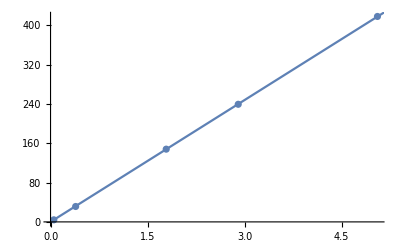

```mathematica
Show[ListPlot[Transpose@{Ptap,PintoFiber}],Plot[82.67 p,{p,0,6}]]
```

### power axes = (tap power, cal factor, √0.2)

```mathematica
pS = 10^-3 T TapCal{5.118,4.811,4.496,4.166,3.866,3.621,3.332,2.865,2.556,2.260,1.979,1.657,1.160,0.854,0.66,0.377};
paS =10^-3 T TapCal {5.129,4.823,4.491,4.168,3.858,3.603,3.328,2.875,2.554,2.261,1.981,1.652,1.159,0.857,0.673,0.377};
```

```mathematica
For[kk=1,kk<17,kk++,If[Length[Subscript[dataCool, kk]]>1809,Subscript[dataS, kk]=Transpose@{Subscript[dataCool, kk][[4;;604,1]]1.0 10^-6,10^(Subscript[dataCool, kk][[607;;1207,3]]/10)-10^(Subscript[dataCool, kk][[4;;604,3]]/10)},
Subscript[dataS, kk]=Transpose@{Subscript[dataCool, kk][[3;;603,1]]1.0 10^-6,10^(Subscript[dataCool, kk][[606;;1206,3]]/10)-10^(Subscript[dataCool, kk][[3;;603,3]]/10)}]]
For[kk=1,kk<17,kk++,If[Length[Subscript[dataCool, kk]]>1809,Subscript[dataAS, kk]=Transpose@{Subscript[dataCool, kk][[4;;604,1]] 1.0 10^-6,10^(Subscript[dataCool, kk][[1210;;1810,3]]/10)-10^(Subscript[dataCool, kk][[4;;604,3]]/10)},Subscript[dataAS, kk]=Transpose@{Subscript[dataCool, kk][[3;;603,1]]1.0 10^-6,10^(Subscript[dataCool, kk][[1209;;1809,3]]/10)-10^(Subscript[dataCool, kk][[3;;603,3]]/10)}]]
```

```mathematica
For[jj=1,jj<2,jj++,fwhm ={};
For[kk=1,kk<Length[Subscript[dataS, jj]],kk++,If[0.53Max[Subscript[dataS, jj][[All,2]]]>Subscript[dataS, jj][[kk,2]]>0.47Max[Subscript[dataS, jj][[All,2]]],fwhm=Append[fwhm,Subscript[dataS, jj][[kk,1]]]]];
Subscript[ΔνSin, jj]=Max[fwhm]-Min[fwhm]]
```

```mathematica
fc =Subscript[dataS, 1][[Position[Subscript[dataS, 1], Max[Subscript[dataS, 1][[All,2]]]][[1]][[1]],1]]
fwhmLow ={};
fwhmHigh = {};
For[pp=1,pp<Length[fwhm]+1,pp++,If[fwhm[[pp]]>fc,fwhmHigh=Append[fwhmHigh,fwhm[[pp]]],fwhmLow=Append[fwhmLow,fwhm[[pp]]]]]
Mean[fwhmHigh]-Mean[fwhmLow]
```

2308.33

67.5926

### Finding FWHM

```mathematica
For[jj=1,jj<17,jj++,fwhmHigh ={};fwhmLow={};fwhm={};Subscript[fc, jj] =Subscript[dataS, jj][[Position[Subscript[dataS, jj], Max[Subscript[dataS, jj][[All,2]]]][[1]][[1]],1]];
For[kk=1,kk<Length[Subscript[dataS, jj]],kk++,
If[0.55Max[Subscript[dataS, jj][[All,2]]]>Subscript[dataS, jj][[kk,2]]>0.45Max[Subscript[dataS, jj][[All,2]]],
If[Subscript[dataS, jj][[kk,1]]>Subscript[fc, jj] ,fwhmHigh=Append[fwhmHigh,Subscript[dataS, jj][[kk,1]]],fwhmLow=Append[fwhmLow,Subscript[dataS, jj][[kk,1]]]]]];
Subscript[ΔνSin, jj]=Mean[fwhmHigh]-Mean[fwhmLow]]
For[jj=1,jj<17,jj++,fwhmHigh ={};fwhmLow={};fwhm={};Subscript[fc, jj] =Subscript[dataAS, jj][[Position[Subscript[dataAS, jj], Max[Subscript[dataAS, jj][[All,2]]]][[1]][[1]],1]];
For[kk=1,kk<Length[Subscript[dataAS, jj]],kk++,
If[0.55Max[Subscript[dataAS, jj][[All,2]]]>Subscript[dataAS, jj][[kk,2]]>0.45Max[Subscript[dataAS, jj][[All,2]]],
If[Subscript[dataAS, jj][[kk,1]]>Subscript[fc, jj] ,fwhmHigh=Append[fwhmHigh,Subscript[dataAS, jj][[kk,1]]],fwhmLow=Append[fwhmLow,Subscript[dataAS, jj][[kk,1]]]]]];
Subscript[ΔνASin, jj]=Mean[fwhmHigh]-Mean[fwhmLow]]
```

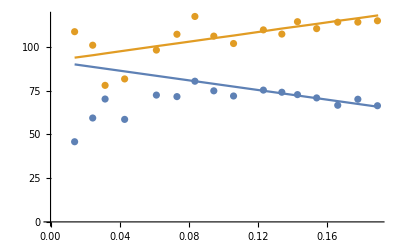

```mathematica
Show[ListPlot[{Table[{pS[[jj]],Subscript[ΔνSin, jj]},{jj,1,16}],Table[{pS[[jj]],Subscript[ΔνASin, jj]},{jj,1,16}]}],ListLinePlot[{Table[{pS[[jj]],92(1-1/4 6 1pS[[jj]])},{jj,1,16}],Table[{paS[[jj]],92(1+1/4 6 1pS[[jj]])},{jj,1,16}]}]]
```

```mathematica
δνs =Table[95(1-1/4 6 1pS[[jj]]),{jj,1,16}];
δνas =Table[95(1+1/4 6 1pS[[jj]]),{jj,1,16}];
```

```mathematica
(*Subscript[dataS, ii][[Position[Subscript[dataS, ii][[All,2]],Max[Subscript[dataS, ii][[All,2]]]][[1]][[1]],1]]*)
```

### Fitting the Stokes

```mathematica
δ=41.40665165183282 (* AOM Frequency*);
Δνin = 60;
fBin = 2268+δ;
For[ii=1,ii<17,ii++,Subscript[fitParsStokes, ii]=FindFit[Subscript[dataS, ii],A (nu/2)^2/((f-fB)^2+(nu/2)^2)+C0,{{A,Max[Subscript[dataS, ii][[All,2]]]},{nu,δνs[[ii]]},{fB,fBin},{C0,Mean[Subscript[dataS, ii][[1;;10,2]]]}},f];Δνin= nu/. Subscript[fitParsStokes, ii]]
```

### Fitting the anti-Stokes Data

```mathematica
(*Subscript[dataAS, ii][[Position[Subscript[dataAS, ii][[All,2]],Max[Subscript[dataAS, ii][[All,2]]]][[1]][[1]],1]]*)
```

```mathematica
Ain =10^-9;
Δνin = 130;
fBin = 2276-δ;
For[ii=1,ii<17,ii++,Subscript[fitParsAntiStokes, ii]=FindFit[Subscript[dataAS, ii],A (nu/2)^2/((f-fB)^2+(nu/2)^2)+C0,{{A,Max[Subscript[dataAS, ii][[All,2]]]},{nu,δνas[[ii]]},{fB,fBin},{C0,Mean[Subscript[dataAS, ii][[1;;10,2]]]}},f];Ain= A/. Subscript[fitParsAntiStokes, ii];Δνin= nu/. Subscript[fitParsAntiStokes, ii];fBin= fB/. Subscript[fitParsAntiStokes, ii]]
```

### Finding integrated scattered power

```mathematica
scattPowerS=Table[{pS[[j]],Sum[Subscript[dataS, j][[nn,2]],{nn,1,Length[Subscript[dataS, 1]]}]},{j,1,16}];
scattPowerAS=Table[{paS[[j]],Sum[Subscript[dataAS, j][[nn,2]],{nn,1,Length[Subscript[dataAS, 1]]}]},{j,1,16}];
```

```mathematica
scattPowerRatio=Table[{pS[[j]],Sum[Subscript[dataS, j][[nn,2]],{nn,1,Length[Subscript[dataS, 1]]}]/Sum[Subscript[dataAS, j][[nn,2]],{nn,1,Length[Subscript[dataAS, 1]]}]},{j,1,16}];
```

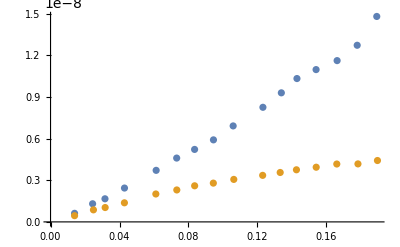

```mathematica
ListPlot[{Table[{pS[[ii]],A/. Subscript[fitParsStokes, ii]},{ii,1,16}],Table[{paS[[ii]],A/. Subscript[fitParsAntiStokes, ii]},{ii,1,16}]}]
```

```mathematica
scattEff=FindFit[Table[{pS[[ii]],(A nu/. Subscript[fitParsStokes, ii])/(A nu/. Subscript[fitParsAntiStokes, ii])},{ii,1,16}],1/2 a x + 1,{a,b},x]
```

{a→10.2619,b→0.}

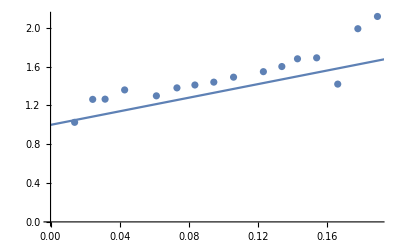

```mathematica
Show[ListPlot[scattPowerRatio],Plot[{1/2 7Pp+1},{Pp,0,0.2}]]
```

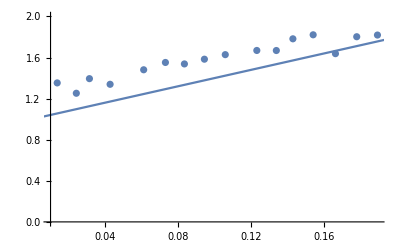

```mathematica
Show[ListPlot[{Table[{pS[[ii]],(A nu/. Subscript[fitParsStokes, ii])/(A nu /. Subscript[fitParsAntiStokes, ii])},{ii,1,16}]},PlotRange->{All,{0,2}}],Plot[{1/2(8)Pp+1.0},{Pp,0,0.2}]]
```

```mathematica
(*δ=((fB/. Subscript[fitParsStokes, 16])-(fB/. Subscript[fitParsAntiStokes, 16]))/2;*)
```

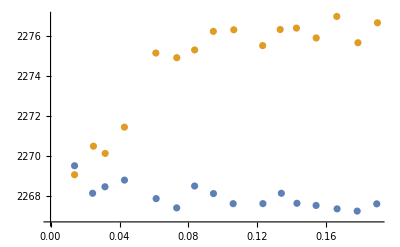

```mathematica
ListPlot[{Table[{pS[[ii]],-δ+fB/. Subscript[fitParsStokes, ii]},{ii,1,16}],Table[{paS[[ii]],δ+fB/. Subscript[fitParsAntiStokes, ii]},{ii,1,16}]}]
```

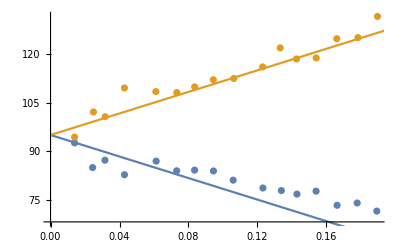

```mathematica
With[{Δν0=95,GB=7,L=1},Show[ListPlot[{Table[{pS[[ii]],Abs[nu/. Subscript[fitParsStokes, ii]]},{ii,1,16}],Table[{paS[[ii]],Abs[nu/. Subscript[fitParsAntiStokes, ii]]},{ii,1,16}]}],Plot[{Δν0(1-1/4 GB Pp L),Δν0(1+1/4 GB Pp L)},{Pp,0,0.2}]]]
```

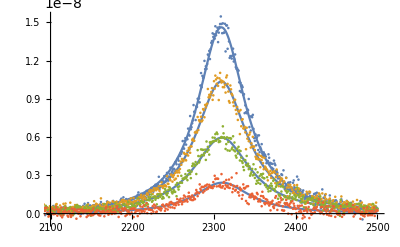

```mathematica
Show[Plot[Table[(C0/. Subscript[fitParsStokes, ii] )+(A/. Subscript[fitParsStokes, ii] )((nu/. Subscript[fitParsStokes, ii])/2)^2/((f-(fB/. Subscript[fitParsStokes, ii]))^2+((nu/. Subscript[fitParsStokes, ii])/2)^2) ,{ii,1,16,4}],{f,2100,2500},PlotRange->{{2100,2500},All}],ListPlot[Table[Subscript[dataS, ii],{ii,1,16,4}]]]
```

### More detailed theory

### Finding full width at half max

```mathematica
Subscript[dataS, 1][[Position[Subscript[dataS, 1][[All,2]],Max[Subscript[dataS, 1][[All,2]]]][[1]][[1]],1]]
```

2308.33

```mathematica
Subscript[dataS, 1][[Position[Subscript[dataS, 1][[All,2]],0.5Max[Subscript[dataS, 1][[All,2]]]][[1]][[1]],1]]
```

Part::partw: Part 1 of {} does not exist.

{}

### Binning data to improve fittie

### Binned Data

```mathematica
NN=3;(* number of data point in a bin = 2 NN *)
For[jj=1,jj<17,jj++,Subscript[aSBinned, jj] = Table[{Mean[Subscript[dataAS, jj][[nn-NN;;nn+NN,1]]],Mean[Subscript[dataAS, jj][[nn-NN;;nn+NN,2]]](*,StandardDeviation[Subscript[dataAS, jj][[nn-NN;;nn+NN,2]]]*)},{nn,1+NN,Length[Subscript[dataAS, jj]]-NN,2NN}]];
For[jj=1,jj<17,jj++,Subscript[SBinned, jj] = Table[{Mean[Subscript[dataS, jj][[nn-NN;;nn+NN,1]]],Mean[Subscript[dataS, jj][[nn-NN;;nn+NN,2]]],StandardDeviation[Subscript[dataS, jj][[nn-NN;;nn+NN,1]]]},{nn,1+NN,Length[Subscript[dataS, jj]]-NN,2NN}]];
```

```mathematica
Lorentzian[f_,a_,fo_,Δν_,c_]= a(Δν^2/4)/((f-fo)^2+Δν^2/4)+c;
```

```mathematica
ain = 10^-9;
fin =2275+40;
Δνin = 60;
cin = 0;
For[jj=1,jj<17,jj++,Subscript[fpS, jj]=FindMinimum[Sum[(Subscript[SBinned, jj][[nn,2]]-Lorentzian[Subscript[SBinned, jj][[nn,1]],a,fo,Δν,c])^2/(Subscript[SBinned, jj][[nn,3]]^2),{nn,1,Length[Subscript[SBinned, jj]]}],{{a,Max[Subscript[SBinned, jj][[All,2]]]},{fo,Subscript[SBinned, jj][[Position[Subscript[SBinned, jj][[All,2]],Max[Subscript[SBinned, jj][[All,2]]]][[1]][[1]],1]]},{Δν,δνs[[jj]]},{c,cin}}]]
ain = 4 10^-9;
fin =2275-40;
Δνin = 130;
cin = 0;
For[jj=1,jj<17,jj++,Subscript[fpAS, jj]=FindMinimum[Sum[(Subscript[aSBinned, jj][[nn,2]]-Lorentzian[Subscript[aSBinned, jj][[nn,1]],a,fo,Δν,c])^2/(Subscript[aSBinned, jj][[nn,3]]^2),{nn,1,Length[Subscript[aSBinned, jj]]}],{{a,Max[Subscript[SBinned, jj][[All,2]]]},{fo,Subscript[aSBinned, jj][[Position[Subscript[aSBinned, jj][[All,2]],Max[Subscript[aSBinned, jj][[All,2]]]][[1]][[1]],1]]},{Δν,δνas[[jj]]},{c,cin}}];Δνin=Δν/.Subscript[fpAS, jj][[2]]]
```

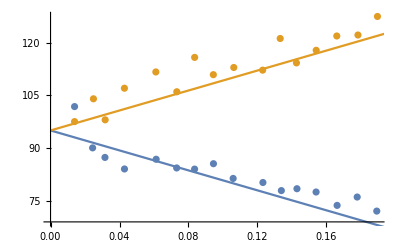

```mathematica
With[{GB=6,L=1,Δν0=95},Show[ListPlot[{Table[{pS[[jj]],Δν/.Subscript[fpS, jj][[2]]},{jj,1,16}],Table[{paS[[jj]],Δν/.Subscript[fpAS, jj][[2]]},{jj,1,16}]}],Plot[{Δν0(1-1/4 GB L Pp),Δν0(1+1/4 GB L Pp)},{Pp,0,0.200}]]]
```

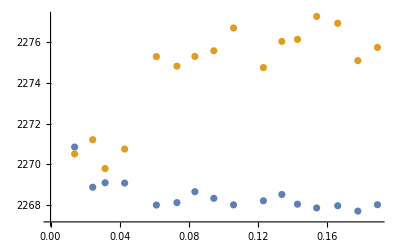

```mathematica
With[{GB=6,L=1,Δν0=95},Show[ListPlot[{Table[{pS[[jj]],(-δ+fo/.Subscript[fpS, jj][[2]])},{jj,1,16}],Table[{pS[[jj]],(δ+fo/.Subscript[fpAS, jj][[2]])},{jj,1,16}]}]]]
```

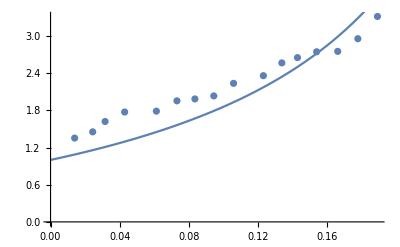

```mathematica
With[{GB=6,L=1,Δν0=95},Show[ListPlot[{Table[{pS[[jj]],(a/.Subscript[fpS, jj][[2]])/a/.Subscript[fpAS, jj][[2]]},{jj,1,16}]}],Plot[{(1+1/2 GB L Pp)/(1-1/2 GB L Pp)},{Pp,0,0.200}]]]
```

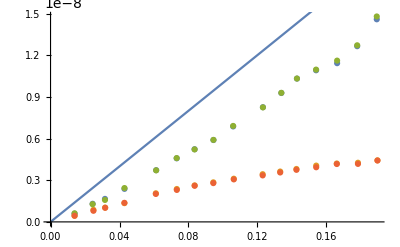

```mathematica
With[{GB=0.1,L=0.75,Δν0=95},Show[ListPlot[{Table[{pS[[jj]],a/.Subscript[fpS, jj][[2]]},{jj,1,16}],Table[{paS[[jj]],a/.Subscript[fpAS, jj][[2]]},{jj,1,16}],Table[{pS[[ii]],A/. Subscript[fitParsStokes, ii]},{ii,1,16}],Table[{paS[[ii]],A/. Subscript[fitParsAntiStokes, ii]},{ii,1,16}]}],Plot[10^-9(1+1/4 GB Pp L)Pp/0.01,{Pp,0,0.2}]]]
```

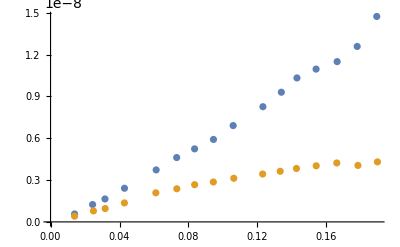

```mathematica
ListPlot[{Table[{pS[[ii]],A/. Subscript[fitParsStokes, ii]},{ii,1,16}],Table[{paS[[ii]],A/. Subscript[fitParsAntiStokes, ii]},{ii,1,16}]}]
```

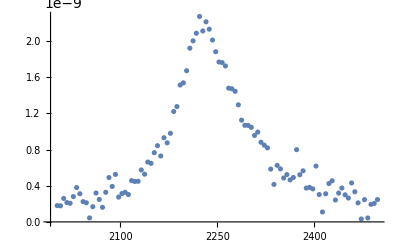

```mathematica
ListPlot[Transpose@{Subscript[aSBinned, 12][[All,1]],Subscript[aSBinned, 12][[All,2]]}]
```

```mathematica
Ain =10^-9;
Δνin = 60;
fBin = 2275+40;
For[ii=1,ii<14,ii++,Subscript[fitParsStokesBin, ii]=FindFit[Subscript[SBinned, ii],A (nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,Ain},{nu,Δνin},{fB,fBin}},f];Ain= A/. Subscript[fitParsStokesBin, ii](*;Δνin= nu/. Subscript[fitParsAntiStokes, ii];fBin= fB/. Subscript[fitParsAntiStokes, ii]*)]
Ain =10^-9;
Δνin = 60;
fBin = 2275+40;
For[ii=1,ii<14,ii++,Subscript[fitParsAntiStokesBin, ii]=FindFit[Subscript[aSBinned, ii],A (nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,Ain},{nu,Δνin},{fB,fBin}},f];Ain= A/. Subscript[fitParsAntiStokesBin, ii](*;Δνin= nu/. Subscript[fitParsAntiStokes, ii];fBin= fB/. Subscript[fitParsAntiStokes, ii]*)]
```

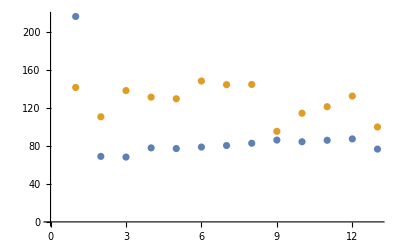

```mathematica
ListPlot[{Table[Abs[nu/. Subscript[fitParsStokesBin, ii]],{ii,1,13}],Table[Abs[nu/. Subscript[fitParsAntiStokesBin, ii]],{ii,1,13}]}]
```

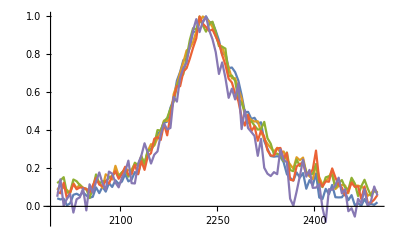

```mathematica
ListLinePlot[Table[Transpose@{Subscript[aSBinned, jj][[All,1]],Subscript[aSBinned, jj][[All,2]]/Max[Subscript[aSBinned, jj][[All,2]]]},{jj,1,13,3}]]
```

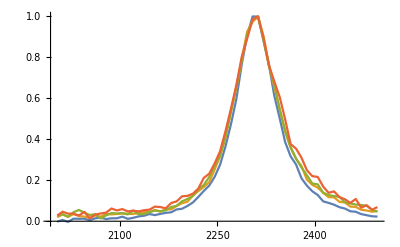

```mathematica
ListLinePlot[Table[Transpose@{Subscript[SBinned, jj][[All,1]],Subscript[SBinned, jj][[All,2]]/Max[Subscript[SBinned, jj][[All,2]]]},{jj,1,10,3}]]
```

```mathematica
Subscript[fitParsAntiStokes, 1]
```

{A→4.30233×10^-9,nu→-118.666,fB→2234.97}

```mathematica
FindFit[Subscript[aSBinned, 1],A (nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,Ain},{nu,Δνin},{fB,fBin}},f]
```

{A→4.25046×10^-9,nu→119.85,fB→2234.61}

#### antiStokes data {freq,data,error} ⟶ used for χ^2 - fitting

```mathematica
aSBinnedError = Table[{Mean[aS[[nn-NN;;nn+NN,1]]],Mean[aS[[nn-NN;;nn+NN,2]]],StandardDeviation[aS[[nn-NN;;nn+NN,2]]]},{nn,3+NN,Length[aS]-NN,2NN}];
```

#### antiStokes data for plotting with errorbars

```mathematica
aSBinnedError2 = Table[{Mean[aS[[nn-NN;;nn+NN,1]]],Around[Mean[aS[[nn-NN;;nn+NN,2]]],StandardDeviation[aS[[nn-NN;;nn+NN,2]]]]},{nn,3+NN,Length[aS]-NN,2NN}];
```

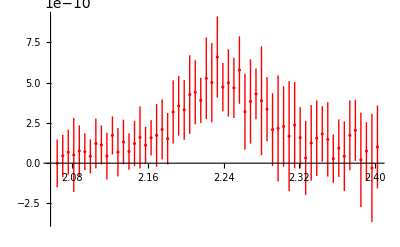

```mathematica
ListPlot[aSBinnedError2,PlotStyle->Red]
```

```mathematica
A/. Subscript[fitParsStokes, 1]
```

1.4724×10^-8

```mathematica
Subscript[fitParsStokes, 2]
```

{A→1.25996×10^-8,Δν→-68.447,fB→2308.62}

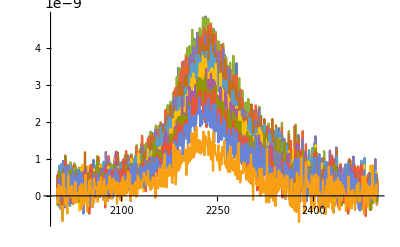

```mathematica
ListLinePlot[Table[Subscript[dataAS, hh],{hh,1,13}],PlotRange->All]
```

```mathematica
"120920d"<>ToString[jj]
```

120920d2

```mathematica
?StringJoin
```

```mathematica
?For
```

```mathematica
dataPumpTap0=Import["/Volumes/BEHUNIN/201206NOPUMP.csv","Data"]
dataPumpTap2pt139=Import["/Volumes/BEHUNIN/ 201206test2.csv","Data"]
```

{{Trace1,},{Freq,,Amp,,},{2000000000,Hz,-83.97,dBm,},{2000750000,Hz,-83.93,dBm,},{2001500000,Hz,-84.06,dBm,},1800,{2447750000,Hz,-83.94,dBm,},{2448500000,Hz,-83.87,dBm,},{2449250000,Hz,-84.,dBm,},{2450000000,Hz,-84.01,dBm,}}
 |  |  |  |

{{Trace1,},{Freq,,Amp,,},{2000000000,Hz,-83.97,dBm,},{2000750000,Hz,-83.93,dBm,},{2001500000,Hz,-84.06,dBm,},1800,{2447750000,Hz,-83.72,dBm,},{2448500000,Hz,-83.76,dBm,},{2449250000,Hz,-83.74,dBm,},{2450000000,Hz,-83.75,dBm,}}
 |  |  |  |

### no pump

```mathematica
dat1p0 = Transpose@{dataPumpTap0[[3;;603,1]],dataPumpTap0[[3;;603,3]]};
dat2p0= Transpose@{dataPumpTap0[[606;;1206,1]],dataPumpTap0[[606;;1206,3]]};
dat3p0= Transpose@{dataPumpTap0[[1209;;1809,1]],dataPumpTap0[[1209;;1809,3]]};
```

### pump tap 2.139 mW

```mathematica
dat1p2pt139 = Transpose@{dataPumpTap2pt139[[3;;603,1]],dataPumpTap2pt139[[3;;603,3]]};
dat2p2pt139= Transpose@{dataPumpTap2pt139[[606;;1206,1]],dataPumpTap2pt139[[606;;1206,3]]};
dat3p2pt139= Transpose@{dataPumpTap2pt139[[1209;;1809,1]],dataPumpTap2pt139[[1209;;1809,3]]};
```

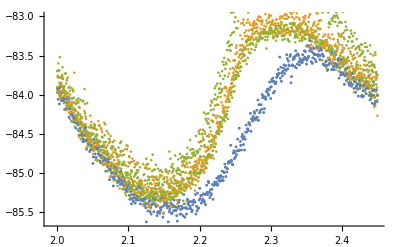

```mathematica
Show[ListPlot[{dat1p0,dat2p0,dat3p0}],ListPlot[{dat1p2pt139,dat2p2pt139,dat3p2pt139}]]
```

### Data background removed

### Stokes

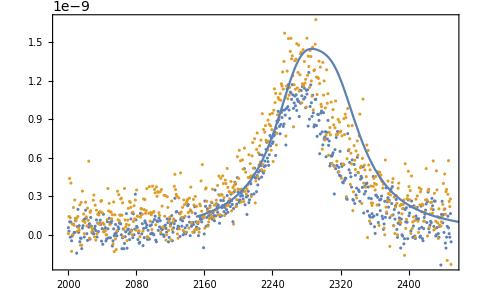

```mathematica
With[{ΔνS =80,ΔνaS =80},Show[ListPlot[{Transpose@{dat1p0[[All,1]] 10^-6,10^(dat2p0[[All,2]]/10)-10^(dat1p0[[All,2]]/10)},Transpose@{dat1p0[[All,1]] 10^-6,10^(dat2p2pt139[[All,2]]/10)-10^(dat1p2pt139[[All,2]]/10)}},PlotRange->All,Frame->True],Plot[{0.75(1.3 10^-9(ΔνS/2)^2/((f-2273)^2+(ΔνS/2)^2)+1.1 10^-9(ΔνS/2)^2/((f-2273-40)^2+(ΔνS/2)^2))},{f,2150,2500}]]]
```

### anti-Stokes

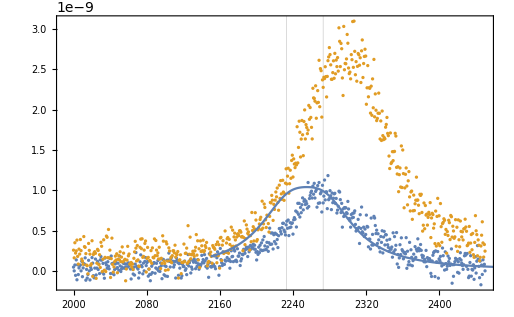

```mathematica
With[{ΔνS =80,ΔνaS =80},Show[ListPlot[{Transpose@{dat1p0[[All,1]] 10^-6,10^(dat3p0[[All,2]]/10)-10^(dat1p0[[All,2]]/10)},Transpose@{dat1p0[[All,1]] 10^-6,10^(dat3p2pt139[[All,2]]/10)-10^(dat1p2pt139[[All,2]]/10)}},PlotRange->All,Frame->True,GridLines->{{2273,2273-40},None}],Plot[{0.5 1.3 10^-9((ΔνS/2)^2/((f-2275)^2+(ΔνS/2)^2)+(ΔνaS/2)^2/((f-2275+40)^2+(ΔνaS/2)^2))},{f,2150,2500}]]]
```

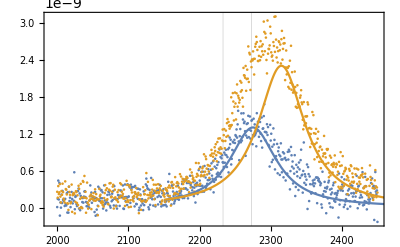

```mathematica
With[{ΔνS =80,ΔνaS =80},Show[ListPlot[{Transpose@{dat1p0[[All,1]] 10^-6,10^(dat2p2pt139[[All,2]]/10)-10^(dat1p2pt139[[All,2]]/10)},Transpose@{dat1p0[[All,1]] 10^-6,10^(dat3p2pt139[[All,2]]/10)-10^(dat1p2pt139[[All,2]]/10)}},PlotRange->All,Frame->True,GridLines->{{2273,2273-40},None}],Plot[{1.3 10^-9((ΔνS/2)^2/((f-2275)^2+(ΔνS/2)^2)+0(ΔνaS/2)^2/((f-2275-40)^2+(ΔνaS/2)^2)),2.3 10^-9((ΔνS/2)^2/((f-2275)^2+(ΔνS/2)^2)0+(ΔνaS/2)^2/((f-2275-40)^2+(ΔνaS/2)^2))},{f,2150,2500}]]]
```

```mathematica
fitPars=FindFit[Transpose@{dat1p0[[All,1]] 10^-6,10^(dat2p0[[All,2]]/10)-10^(dat1p0[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
```

{A→1.08725×10^-9,fB→2273.22,nu→88.9585}

```mathematica
FindFit[Transpose@{dat1p0[[All,1]] 10^-6,10^(dat3p0[[All,2]]/10)-10^(dat1p0[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
```

{A→9.59714×10^-10,fB→2273.91,nu→95.2435}

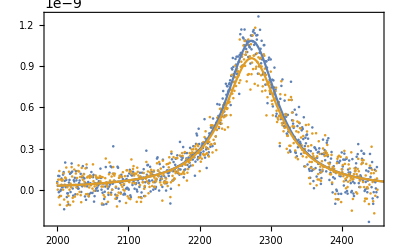

```mathematica
With[{As=1.0872494880768342*^-9,AaS=9.597138207662346*^-10,fB=2273,ΔνS =89,ΔνaS =95},Show[ListPlot[{Transpose@{dat1p0[[All,1]] 10^-6,10^(dat2p0[[All,2]]/10)-10^(dat1p0[[All,2]]/10)},Transpose@{dat1p0[[All,1]] 10^-6,10^(dat3p0[[All,2]]/10)-10^(dat1p0[[All,2]]/10)}},PlotRange->All,Frame->True],Plot[{As(ΔνS/2)^2/((f-fB)^2+(ΔνS/2)^2),AaS(ΔνaS/2)^2/((f-fB)^2+(ΔνaS/2)^2)},{f,2000,2500}]]]
```

### Spontaneous Spectra

```mathematica
dat4mW=Import["/Users/ryanbehunin/Sync/Current Projects Shared/CloudStation/Brillouin Cooling/Cooling Data/201208 Cooling Data/201208 4.013.csv","Data"];
dat3pt5mW=Import["/Users/ryanbehunin/Sync/Current Projects Shared/CloudStation/Brillouin Cooling/Cooling Data/201208 Cooling Data/201208 3.545.csv","Data"];
dat3mW=Import["/Users/ryanbehunin/Sync/Current Projects Shared/CloudStation/Brillouin Cooling/Cooling Data/201208 Cooling Data/201208  3.055.csv","Data"];
dat2pt5mW=Import["/Users/ryanbehunin/Sync/Current Projects Shared/CloudStation/Brillouin Cooling/Cooling Data/201208 Cooling Data/201208 2.547.csv","Data"];
dat2mW=Import["/Users/ryanbehunin/Sync/Current Projects Shared/CloudStation/Brillouin Cooling/Cooling Data/201208 Cooling Data/20120 2.49.csv","Data"];
dat1pt5mW=Import["/Users/ryanbehunin/Sync/Current Projects Shared/CloudStation/Brillouin Cooling/Cooling Data/201208 Cooling Data/201208 1.52.csv","Data"];
dat1mW=Import["/Users/ryanbehunin/Sync/Current Projects Shared/CloudStation/Brillouin Cooling/Cooling Data/201208 Cooling Data/201208  1.026.csv","Data"];
dat0pt5mW=Import["/Users/ryanbehunin/Sync/Current Projects Shared/CloudStation/Brillouin Cooling/Cooling Data/201208 Cooling Data/201208 .4980.csv","Data"];
```

```mathematica
dat1p4mW = Transpose@{dat4mW[[3;;603,1]],dat4mW[[3;;603,3]]};
dat2p4mW= Transpose@{dat4mW[[606;;1206,1]],dat4mW[[606;;1206,3]]};
dat3p4mW= Transpose@{dat4mW[[1209;;1809,1]],dat4mW[[1209;;1809,3]]};
dat1p3pt5mW = Transpose@{dat3pt5mW[[3;;603,1]],dat3pt5mW[[3;;603,3]]};
dat2p3pt5mW= Transpose@{dat3pt5mW[[606;;1206,1]],dat3pt5mW[[606;;1206,3]]};
dat3p3pt5mW= Transpose@{dat3pt5mW[[1209;;1809,1]],dat3pt5mW[[1209;;1809,3]]};
dat1p3mW = Transpose@{dat3mW[[3;;603,1]],dat3mW[[3;;603,3]]};
dat2p3mW= Transpose@{dat3mW[[606;;1206,1]],dat3mW[[606;;1206,3]]};
dat3p3mW= Transpose@{dat3mW[[1209;;1809,1]],dat3mW[[1209;;1809,3]]};
dat1p2pt5mW = Transpose@{dat2pt5mW[[3;;603,1]],dat2pt5mW[[3;;603,3]]};
dat2p2pt5mW= Transpose@{dat2pt5mW[[606;;1206,1]],dat2pt5mW[[606;;1206,3]]};
dat3p2pt5mW= Transpose@{dat2pt5mW[[1209;;1809,1]],dat2pt5mW[[1209;;1809,3]]};
dat1p2mW = Transpose@{dat2mW[[3;;603,1]],dat2mW[[3;;603,3]]};
dat2p2mW= Transpose@{dat2mW[[606;;1206,1]],dat2mW[[606;;1206,3]]};
dat3p2mW= Transpose@{dat2mW[[1209;;1809,1]],dat2mW[[1209;;1809,3]]};
dat1p1pt5mW = Transpose@{dat1pt5mW[[3;;603,1]],dat1pt5mW[[3;;603,3]]};
dat2p1pt5mW= Transpose@{dat1pt5mW[[606;;1206,1]],dat1pt5mW[[606;;1206,3]]};
dat3p1pt5mW= Transpose@{dat1pt5mW[[1209;;1809,1]],dat1pt5mW[[1209;;1809,3]]};
dat1p1mW = Transpose@{dat1mW[[3;;603,1]],dat1mW[[3;;603,3]]};
dat2p1mW= Transpose@{dat1mW[[606;;1206,1]],dat1mW[[606;;1206,3]]};
dat3p1mW= Transpose@{dat1mW[[1209;;1809,1]],dat1mW[[1209;;1809,3]]};
dat1p0pt5mW = Transpose@{dat0pt5mW[[3;;603,1]],dat0pt5mW[[3;;603,3]]};
dat2p0pt5mW= Transpose@{dat0pt5mW[[606;;1206,1]],dat0pt5mW[[606;;1206,3]]};
dat3p0pt5mW= Transpose@{dat0pt5mW[[1209;;1809,1]],dat0pt5mW[[1209;;1809,3]]};
```

### power = 4mW

```mathematica
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6+40,10^(dat2p4mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
```

{A→4.62425×10^-9,fB→2275.41,nu→114.918}

```mathematica
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6-40,10^(dat3p4mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-8},{fB,2275},{nu,60}},f ]
```

{A→1.21246×10^-8,fB→2272.1,nu→71.1794}

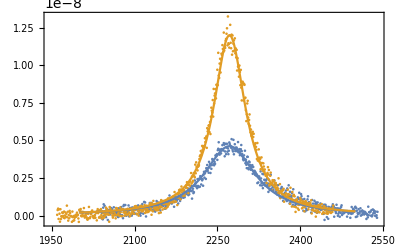

```mathematica
With[{As=1.2*^-8,AaS=4.62 10^-9,fB=2272,ΔνS =71,ΔνaS =114},Show[ListPlot[{Transpose@{dat1p4mW[[All,1]] 10^-6+40,10^(dat2p4mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},Transpose@{dat1p4mW[[All,1]] 10^-6-40,10^(dat3p4mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)}},PlotRange->All,Frame->True],Plot[{AaS(ΔνaS/2)^2/((f-fB)^2+(ΔνaS/2)^2),As(ΔνS/2)^2/((f-fB)^2+(ΔνS/2)^2)},{f,2000,2500},PlotRange->All]]]
```

### power = 3mW

```mathematica
FindFit[Transpose@{dat1p3mW[[All,1]] 10^-6+40,10^(dat2p3mW[[All,2]]/10)- 10^(dat1p3mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
```

{A→4.61392×10^-9,fB→2275.61,nu→115.099}

```mathematica
FindFit[Transpose@{dat1p3mW[[All,1]] 10^-6-40,10^(dat3p3mW[[All,2]]/10)- 10^(dat1p3mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
```

{A→1.43806×10^-8,fB→2270.93,nu→69.6375}

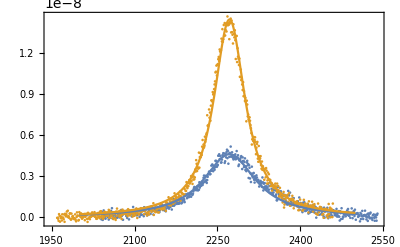

```mathematica
With[{As=1.44*^-8,AaS=4.6 10^-9,fB=2272,ΔνS =69.6,ΔνaS =115},Show[ListPlot[{Transpose@{dat1p3mW[[All,1]] 10^-6+40,10^(dat2p3mW[[All,2]]/10)- 10^(dat1p3mW[[All,2]]/10)},Transpose@{dat1p3mW[[All,1]] 10^-6-40,10^(dat3p3mW[[All,2]]/10)- 10^(dat1p3mW[[All,2]]/10)}},PlotRange->All,Frame->True],Plot[{AaS(ΔνaS/2)^2/((f-fB)^2+(ΔνaS/2)^2),As(ΔνS/2)^2/((f-fB)^2+(ΔνS/2)^2)},{f,2000,2500},PlotRange->All]]]
```

### power 2mW

```mathematica
FindFit[Transpose@{dat1p2mW[[All,1]] 10^-6+40,10^(dat2p2mW[[All,2]]/10)- 10^(dat1p2mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
```

{A→3.89662×10^-9,fB→2275.06,nu→102.539}

```mathematica
FindFit[Transpose@{dat1p2mW[[All,1]] 10^-6-40,10^(dat3p2mW[[All,2]]/10)- 10^(dat1p2mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-8},{fB,2275},{nu,100}},f ]
```

{A→1.03434×10^-8,fB→2270.16,nu→70.1892}

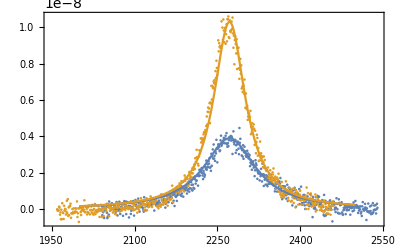

```mathematica
With[{As=1.03*^-8,AaS=3.9 10^-9,fB=2272,ΔνS =70,ΔνaS =114},Show[ListPlot[{Transpose@{dat1p2mW[[All,1]] 10^-6+40,10^(dat2p2mW[[All,2]]/10)- 10^(dat1p2mW[[All,2]]/10)},Transpose@{dat1p2mW[[All,1]] 10^-6-40,10^(dat3p2mW[[All,2]]/10)- 10^(dat1p2mW[[All,2]]/10)}},PlotRange->All,Frame->True],Plot[{AaS(ΔνaS/2)^2/((f-fB)^2+(ΔνaS/2)^2),As(ΔνS/2)^2/((f-fB)^2+(ΔνS/2)^2)},{f,2000,2500},PlotRange->All]]]
```

### power 1mW

```mathematica
FindFit[Transpose@{dat1p1mW[[All,1]] 10^-6+40,10^(dat2p1mW[[All,2]]/10)- 10^(dat1p1mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
```

{A→2.02327×10^-9,fB→2274.89,nu→98.431}

```mathematica
FindFit[Transpose@{dat1p1mW[[All,1]] 10^-6-40,10^(dat3p1mW[[All,2]]/10)- 10^(dat1p1mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-8},{fB,2275},{nu,100}},f ]
```

{A→3.80343×10^-9,fB→2272.59,nu→72.2022}

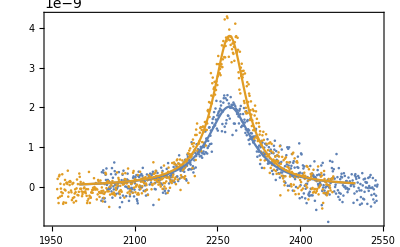

```mathematica
With[{As=3.8*^-9,AaS=2.02 10^-9,fB=2272,ΔνS =72,ΔνaS =98},Show[ListPlot[{Transpose@{dat1p1mW[[All,1]] 10^-6+40,10^(dat2p1mW[[All,2]]/10)- 10^(dat1p1mW[[All,2]]/10)},Transpose@{dat1p1mW[[All,1]] 10^-6-40,10^(dat3p1mW[[All,2]]/10)- 10^(dat1p1mW[[All,2]]/10)}},PlotRange->All,Frame->True],Plot[{AaS(ΔνaS/2)^2/((f-fB)^2+(ΔνaS/2)^2),As(ΔνS/2)^2/((f-fB)^2+(ΔνS/2)^2),},{f,2000,2500},PlotRange->All]]]
```

### Low power

```mathematica
FindFit[Transpose@{dat1p0pt5mW[[All,1]] 10^-6+40,10^(dat2p0pt5mW[[All,2]]/10)- 10^(dat1p0pt5mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
```

{A→9.68931×10^-10,fB→2272.85,nu→56.1064}

```mathematica
FindFit[Transpose@{dat1p0pt5mW[[All,1]] 10^-6-40,10^(dat3p0pt5mW[[All,2]]/10)- 10^(dat1p0pt5mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,1.5 10^-9},{fB,2275},{nu,60}},f ]
```

{A→1.66932×10^-9,fB→2271.77,nu→55.8686}

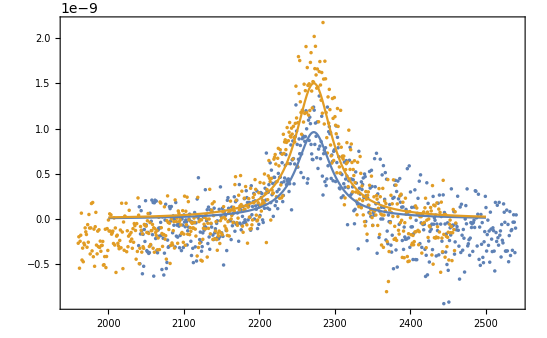

```mathematica
With[{As=1.5*^-9,AaS=0.96 10^-9,fB=2272,ΔνS =60,ΔνaS =56},Show[ListPlot[{Transpose@{dat1p0pt5mW[[All,1]] 10^-6+40,10^(dat2p0pt5mW[[All,2]]/10)- 10^(dat1p0pt5mW[[All,2]]/10)},Transpose@{dat3p0pt275mW[[All,1]] 10^-6-40,10^(dat3p0pt5mW[[All,2]]/10)- 10^(dat1p0pt5mW[[All,2]]/10)}},PlotRange->All,Frame->True],Plot[{AaS(ΔνaS/2)^2/((f-fB)^2+(ΔνaS/2)^2),As(ΔνS/2)^2/((f-fB)^2+(ΔνS/2)^2)},{f,2000,2500},PlotRange->All]]]
```

### collecting amplitudes and linewidths

#### anti-Stokes

```mathematica
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6+40,10^(dat2p4mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6+40,10^(dat2p3pt5mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6+40,10^(dat2p3mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6+40,10^(dat2p2pt5mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6+40,10^(dat2p2mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6+40,10^(dat2p1pt5mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6+40,10^(dat2p1mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6+40,10^(dat2p0pt5mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
```

{A→4.62425×10^-9,fB→2275.41,nu→114.918}

{A→4.82571×10^-9,fB→2274.28,nu→114.397}

{A→4.61392×10^-9,fB→2275.61,nu→115.099}

{A→2.85224×10^-9,fB→2274.66,nu→101.016}

{A→3.89662×10^-9,fB→2275.06,nu→102.539}

{A→2.58187×10^-9,fB→2271.91,nu→92.9559}

{A→2.02327×10^-9,fB→2274.89,nu→98.431}

{A→9.68931×10^-10,fB→2272.85,nu→56.1064}

```mathematica
ampAS ={9.689314317512843*^-10,2.0232734817828476*^-9,2.581873467571612*^-9,3.8966204621194035*^-9,2.8522410774466067*^-9,4.613920483278896*^-9,4.825712454279459*^-9,4.624254953849178*^-9};
```

```mathematica
lwAS ={56.1,98.4,93,102.5,101,115,114.4,115};
```

#### Stokes

```mathematica
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6-40,10^(dat3p4mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6-40,10^(dat3p3pt5mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6-40,10^(dat3p3mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6-40,10^(dat3p2pt5mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6-40,10^(dat3p2mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6-40,10^(dat3p1pt5mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6-40,10^(dat3p1mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6-40,10^(dat3p0pt5mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
```

{A→1.21204×10^-8,fB→2272.07,nu→-71.3334}

{A→1.75534×10^-8,fB→2269.92,nu→66.5135}

{A→1.43806×10^-8,fB→2270.93,nu→69.6375}

{A→5.7047×10^-9,fB→2272.23,nu→-76.9931}

{A→1.03522×10^-8,fB→2270.19,nu→70.0439}

{A→5.77713×10^-9,fB→2271.91,nu→-70.3254}

{A→3.79769×10^-9,fB→2272.53,nu→72.3255}

{A→1.1225×10^-9,fB→2272.11,nu→83.2292}

```mathematica
pwr={0.5,1,1.5,2,2.5,3,3.5,4};
ampS ={1.1224975561263412*^-9,3.797686387178483*^-9,5.777126629610562*^-9,1.0352249086561439*^-8,5.704704053127763*^-9,1.4380557158113891*^-8,1.755344930876738*^-8,1.2120413536840679*^-8};
lwS={83.2,72.3,70.3,70,77,69.6,66.5,71.3};
```

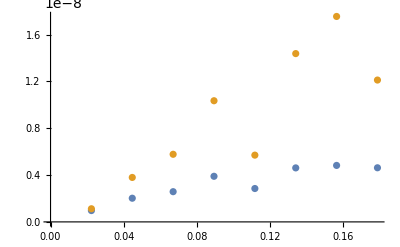

```mathematica
ListPlot[{Transpose@{√0.2/10pwr,ampAS},Transpose@{√0.2/10pwr,ampS}}]
```

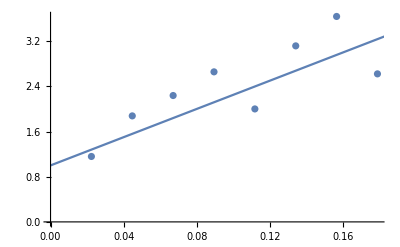

```mathematica
With[{GB=25,L=1},Show[ListPlot[{Transpose@{√0.2 pwr/10,ampS/ampAS}}],Plot[1+1/2 GB Pp L,{Pp,0,0.4}]]]
```

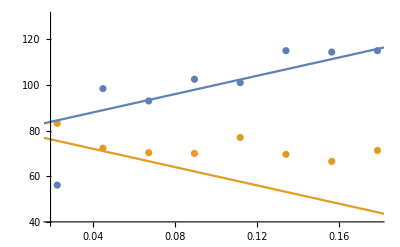

```mathematica
With[{GB=10,L=1,Δν0=80},Show[ListPlot[{Transpose@{√0.2 pwr/10,lwAS},Transpose@{√0.2 pwr/10,lwS}},PlotRange->{All,{40,130}}],Plot[{Δν0(1+1/4 GB L Pp),Δν0(1-1/4 GB L Pp)},{Pp,0,0.4}]]]
```

```mathematica
With[{x=100},Plot[{x+P]
```

### Two-mode spectroscopy

```mathematica
hpDat=Import["/Users/ryanbehunin/Downloads/20201220 Data/20201220 1.csv","Data"];
hpDatz=Import["/Users/ryanbehunin/Downloads/20201220 Data/20201220 1z.csv","Data"];
hpDat0=Import["/Users/ryanbehunin/Downloads/20201220 Data/20201220 0.csv","Data"];
```

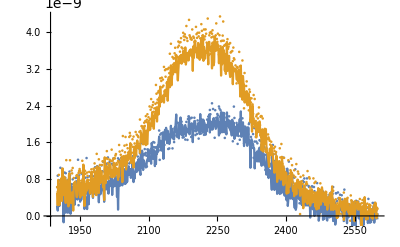

```mathematica
Show[ListPlot[{Transpose@{hpDat[[606;;1206,1]] 10^-6,10^(hpDat[[1209;;1809,3]]/10)-10^(hpDat[[3;;603,3]]/10)-(10^(hpDatz[[1209;;1809,3]]/10)- 10^(hpDatz[[3;;603,3]]/10))},Transpose@{hpDat[[606;;1206,1]] 10^-6,10^(hpDat[[606;;1206,3]]/10)-10^(hpDat[[3;;603,3]]/10)-((10^(hpDatz[[606;;1206,3]]/10)- 10^(hpDatz[[3;;603,3]]/10)))}}],ListLinePlot[{Transpose@{hpDat0[[606;;1206,1]] 10^-6,10^(hpDat0[[1209;;1809,3]]/10)-10^(hpDat0[[3;;603,3]]/10)},Transpose@{hpDat0[[606;;1206,1]] 10^-6,10^(hpDat0[[606;;1206,3]]/10)-10^(hpDat0[[3;;603,3]]/10)}}]]
```

```mathematica
FindFit[Transpose@{dat1p4mW[[All,1]] 10^-6-40,10^(dat3p1mW[[All,2]]/10)- 10^(dat1p4mW[[All,2]]/10)},A(nu/2)^2/((f-fB)^2+(nu/2)^2),{{A,10^-9},{fB,2275},{nu,100}},f ]
```

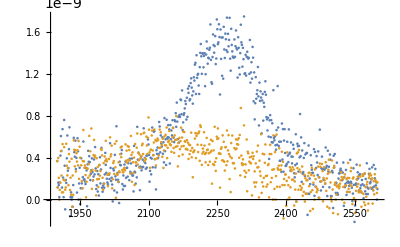

```mathematica
ListPlot[{Transpose@{hpDatz[[606;;1206,1]] 10^-6,10^(hpDatz[[606;;1206,3]]/10)- 10^(hpDatz[[3;;603,3]]/10)},Transpose@{hpDatz[[606;;1206,1]] 10^-6,10^(hpDatz[[1209;;1809,3]]/10)- 10^(hpDatz[[3;;603,3]]/10)}},PlotRange->All]
```

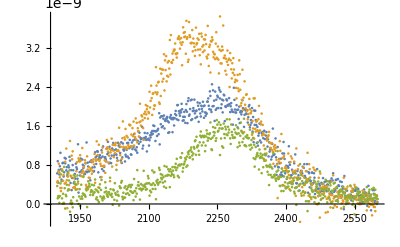

```mathematica
ListPlot[{Transpose@{hpDat[[606;;1206,1]] 10^-6,10^(hpDat[[1209;;1809,3]]/10)-10^(hpDat[[3;;603,3]]/10)-(10^(hpDatz[[1209;;1809,3]]/10)-10^(hpDatz[[3;;603,3]]/10))},Transpose@{hpDat[[606;;1206,1]] 10^-6,10^(hpDat[[606;;1206,3]]/10)- 10^(hpDat[[3;;603,3]]/10)-1.5(10^(hpDatz[[606;;1206,3]]/10)-  10^(hpDatz[[3;;603,3]]/10))},Transpose@{hpDat[[606;;1206,1]] 10^-6,(10^(hpDatz[[606;;1206,3]]/10)- 10^(hpDatz[[3;;603,3]]/10))}}]
```

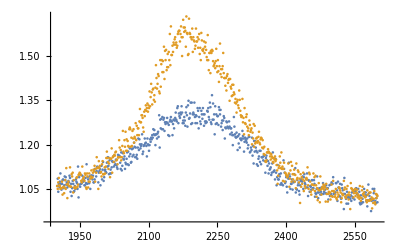

```mathematica
ListPlot[{Transpose@{hpDat[[606;;1206,1]] 10^-6,10^((hpDat[[1209;;1809,3]]-hpDatz[[1209;;1809,3]])/10)},Transpose@{hpDat[[606;;1206,1]] 10^-6,10^((hpDat[[606;;1206,3]]-hpDatz[[606;;1206,3]])/10)}},PlotRange->All]
```

```mathematica
hpDat[[608]]
```

{1900000000,Hz,-79.65,dBm,}

```mathematica
Length[hpDat]
```

1809

Part::partw: Part 3 of {Trace2,} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

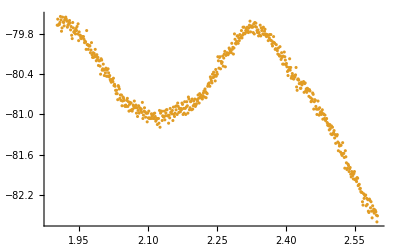

```mathematica
ListPlot[{Transpose@{hpDat[[603;;1203,1]],hpDat[[603;;1203,3]]-0hpDat[[3;;603,3]]},Transpose@{hpDat[[608;;1208,1]],hpDat[[603;;1203,3]]0+hpDat[[1209;;1809,3]]}}]
```

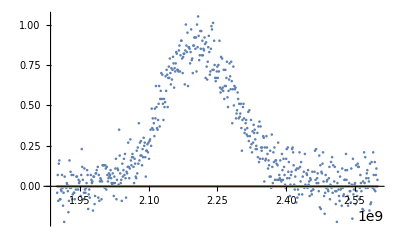

```mathematica
ListPlot[{Transpose@{hpDat[[608;;1208,1]],hpDat[[608;;1208,3]]-hpDat[[1211;;1811,3]]},Transpose@{hpDat[[608;;1208,1]],hpDat[[608;;1208,3]]0+0hpDat[[1211;;1811,3]]}},PlotRange->All]
```

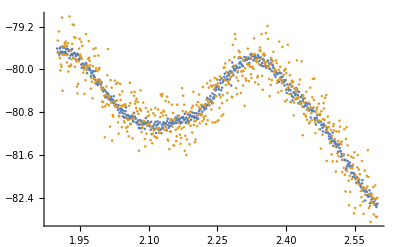

```mathematica
ListPlot[{Transpose@{hpDat[[1211;;1811,1]],hpDat[[1211;;1811,3]]-0hpDat[[3;;603,3]]},Transpose@{hpDat[[608;;1208,1]],hpDat[[608;;1208,3]]0+hpDat[[3;;603,3]]}}]
```